# Correction Procedure via Reconstruction (CPR)

## CPR: Flux Reconstruction (FR) / Lifting Collocation Penalty (LCP)

## Coded by Manuel Diaz, NTU, 2013.08.20

Based on Ideas of jounal papers:

1. Z.J. Wang & Hai - Yang Gao, JCP 228 (2009) 8161-8186. -> (LCP)
2. H.T. Huynh, AIAA (2007) 4079.->  (FR)
3. Jie Du, Chi-Wang Shu, MengPing Zhang, Brown University (2013) 15.  -> (CPR)

Derivation of the Method in one-dimensional space.

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Change Notebook to it’s original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Symbolize[u^+];Symbolize[u^-];
```

## Review on Flux Reconstruction Method

### Building the Domain

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nf = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Therefore the Jacobian metric between this two elements is given by,

```mathematica
J = Subscript[h, j]/2;
```

Now, let us define solution points, ξ_k, inside the standar element:
We can use for example: four-Gauss Legendre points,

```mathematica
abscissas = {-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}; weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)};
```

Or we can use also: four Legendre-Gauss-Lobatto (LGL) points,

```mathematica
(* abscissas = {-1,-1/(√5),1/(√5),1}; weights={1/6,5/6,5/6,1/6}; *)
```

I, personally, prefer to call the abscissas ‘standar solution points’ or simply ‘solution points’. I will also  referer to all the points inside the domain as my ‘global nodes coordinates’.

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ J ×abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0.00694318 | 0.0330009 | 0.0669991 | 0.0930568
0.106943 | 0.133001 | 0.166999 | 0.193057
0.206943 | 0.233001 | 0.266999 | 0.293057
0.306943 | 0.333001 | 0.366999 | 0.393057
0.406943 | 0.433001 | 0.466999 | 0.493057
0.506943 | 0.533001 | 0.566999 | 0.593057
0.606943 | 0.633001 | 0.666999 | 0.693057
0.706943 | 0.733001 | 0.766999 | 0.793057
0.806943 | 0.833001 | 0.866999 | 0.893057
0.906943 | 0.933001 | 0.966999 | 0.993057

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u(x) = 0.5 +sin(2πx), therefore

```mathematica
Subscript[u, 𝒟]=0.5(2+Sin[2 π Subscript[x, 𝒟]]);
Subscript[u, 𝒟]//TableForm
```

1.02181 | 1.10293 | 1.20432 | 1.27597
1.31125 | 1.37087 | 1.43353 | 1.46834
1.48181 | 1.49715 | 1.49715 | 1.48181
1.46834 | 1.43353 | 1.37087 | 1.31125
1.27597 | 1.20432 | 1.10293 | 1.02181
0.978194 | 0.897066 | 0.795678 | 0.724028
0.688746 | 0.629127 | 0.566466 | 0.531663
0.518186 | 0.502849 | 0.502849 | 0.518186
0.531663 | 0.566466 | 0.629127 | 0.688746
0.724028 | 0.795678 | 0.897066 | 0.978194

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=4 and k=1, we should get

```mathematica
Subscript[u, 4,1]
```

1.46834

### Compute Fluxes in nodes

Let us compute the fluxes,' f_(j,k)’  at every node as well. 
Assume Burgers’ Flux: f(u) = u^2/2,

```mathematica
Subscript[f, 𝒟]= Subscript[u, 𝒟]^2/2;
```

```mathematica
Subscript[f, 𝒟] //TableForm
```

0.522043 | 0.608232 | 0.725196 | 0.814052
0.859694 | 0.939646 | 1.02751 | 1.07801
1.09789 | 1.12073 | 1.12073 | 1.09789
1.07801 | 1.02751 | 0.939646 | 0.859694
0.814052 | 0.725196 | 0.608232 | 0.522043
0.478432 | 0.402364 | 0.316552 | 0.262108
0.237185 | 0.1979 | 0.160442 | 0.141333
0.134258 | 0.126429 | 0.126429 | 0.134258
0.141333 | 0.160442 | 0.1979 | 0.237185
0.262108 | 0.316552 | 0.402364 | 0.478432

```mathematica
Table[Subscript[f, j,k]= Subscript[f, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j = 4 and k = 1, we should get

```mathematica
Subscript[f, 4,1]
```

1.07801

```mathematica
(*Ok!*)
```

## Intermision I: Interpolation of data

Compute the Lagrange polynomial for every value of u_(j,k) inside of I_j for ξ_k ∈ [-1,1]:

#### Interpolate u_j :

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, k],Subscript[u, j,k]},{k,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-√(1/35 (15+2 √30)),u_(j,1)},{-√(1/35 (15-2 √30)),u_(j,2)},{√(1/35 (15-2 √30)),u_(j,3)},{√(1/35 (15+2 √30)),u_(j,4)}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],u,Simplify]
```

```mathematica
Subscript[u, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing: interpolate 'u' at the boundaries of Subscript[I, j] *)
```

```mathematica
Subscript[u, j][-1]//N //Expand
Subscript[u, j][1]//N //Expand
```

-0.113917 u_(j,1)+0.400762 u_(j,2)-0.813632 u_(j,3)+1.52679 u_(j,4)

1.52679 u_(j,1)-0.813632 u_(j,2)+0.400762 u_(j,3)-0.113917 u_(j,4)

```mathematica
(* Everything seems fine *)
```

This result comes from interpolating ' u' values over the selected gauss Lobatto/ Solution points. ( equations 2.2 and 2.3 in [1], equations 6, 7 and 11 in [3] )

Notice that the lagrange coeficients of this lagrange polynomial can be copied directly to code. This is because we are performing our interpolation inside our standard element.

#### Interpolate f_j :

Similarly for the flux values f_j :

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, k],Subscript[f, j,k]},{k,1,r}]
```

```mathematica
StencilPoints[4]//N
```

{{-0.861136,f_(j,1)},{-0.339981,f_(j,2)},{0.339981,f_(j,3)},{0.861136,f_(j,4)}}

{{-0.861136,f_(j,1)},{-0.339981,f_(j,2)},{0.339981,f_(j,3)},{0.861136,f_(j,4)}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],f,Simplify]
```

```mathematica
Subscript[f, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing: interpolate flux at the boundaries of Subscript[I, j] *)
```

```mathematica
Subscript[f, j][-1]//N //Expand
Subscript[f, j][1]//N //Expand
```

-0.113917 f_(j,1)+0.400762 f_(j,2)-0.813632 f_(j,3)+1.52679 f_(j,4)

1.52679 f_(j,1)-0.813632 f_(j,2)+0.400762 f_(j,3)-0.113917 f_(j,4)

```mathematica
(* So far so good! *)
```

Notice that we are interpolating in same standard element, therefore lagrange coeficients are the same as before.

#### Interpolate for d/dxf_j :

```mathematica
Subscript[df, j][ξ_] := Evaluate[D[LagrangePolynomials[4],ξ]]
```

```mathematica
Subscript[df, j][abscissas]//N //Expand//MatrixForm
```

(-3.332 f_(j,1)+4.86015 f_(j,2)-2.10878 f_(j,3)+0.580628 f_(j,4)
-0.757558 f_(j,1)-0.384414 f_(j,2)+1.47067 f_(j,3)-0.328698 f_(j,4)
0.328698 f_(j,1)-1.47067 f_(j,2)+0.384414 f_(j,3)+0.757558 f_(j,4)
-0.580628 f_(j,1)+2.10878 f_(j,2)-4.86015 f_(j,3)+3.332 f_(j,4))

Again the last coeficients, can be copied directly into any code. It would let us compute the slope of the flux in every solution point ξ_k, and therefore any global node x_(j,k) (of course by using the appropiate Jacobian metric)

```mathematica
Subscript[df, j] = Table[
{0.007607257743127306 (-438.0028058550456 Subscript[f, j,1]+638.8838895429894 Subscript[f, j,2]-277.20663867348725 Subscript[f, j,3]+76.32555498554348 Subscript[f, j,4]),0.007607257743127306 (-99.58353461648397 Subscript[f, j,1]-50.532584172069605 Subscript[f, j,2]+193.3246224777092 Subscript[f, j,3]-43.20850368915568 Subscript[f, j,4]),0.007607257743127306 (43.208503689155656 Subscript[f, j,1]-193.32462247770923 Subscript[f, j,2]+50.53258417206956 Subscript[f, j,3]+99.58353461648397 Subscript[f, j,4]),0.007607257743127306 (-76.32555498554348 Subscript[f, j,1]+277.20663867348725 Subscript[f, j,2]-638.8838895429894 Subscript[f, j,3]+438.0028058550456 Subscript[f, j,4])}
,{j,1,n}]
```

{{0.160034,0.169655,0.172553,0.167375},{0.161453,0.144308,0.112312,0.0804124},{0.062851,0.0248139,-0.0248139,-0.062851},{-0.0804124,-0.112312,-0.144308,-0.161453},{-0.167375,-0.172553,-0.169655,-0.160034},{-0.153938,-0.137725,-0.114235,-0.0944397},{-0.0847504,-0.0662559,-0.0443402,-0.0292401},{-0.0215421,-0.00850492,0.00850492,0.0215421},{0.0292401,0.0443402,0.0662559,0.0847504},{0.0944397,0.114235,0.137725,0.153938}}

## Intermission II: Values at the faces of I_j

### Compute u values at I_j faces

If the solutions points ξ_k include points the at the boundaries for the standar element, we can just simply do: (u_(j+1/2))^- = u_(j,1) and (u_(j-1/2))^+ = u_(j,k)

At the boundary cells at ξ_1 and ξ_K (or ξ_4 for our example) immediatly we recognize them as (u_(j-1/2))^+= u_(j,1), and (u_(j+1/2))^-= u_(j,K)

```mathematica
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,1]];
SuperMinus[Subscript[u, j+1/2]] // TableForm
```

1.02181
1.31125
1.48181
1.46834
1.27597
0.978194
0.688746
0.518186
0.531663
0.724028

```mathematica
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,4]];
SuperMinus[Subscript[u, j+1/2]] // TableForm
```

1.27597
1.46834
1.48181
1.31125
1.02181
0.724028
0.531663
0.518186
0.688746
0.978194

But in this example we have to interpolate these values as showed before:

```mathematica
SuperPlus[Subscript[u, j-1/2]] = Subscript[u, j][-1] //N //Expand
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, j][1] //N // Expand
```

1.52679 u_(j,1)-0.813632 u_(j,2)+0.400762 u_(j,3)-0.113917 u_(j,4)

-0.113917 u_(j,1)+0.400762 u_(j,2)-0.813632 u_(j,3)+1.52679 u_(j,4)

```mathematica
SuperPlus[Subscript[u, j-1/2]] = Table[1.526788125457267 Subscript[u, j,1]-0.8136324494869269 Subscript[u, j,2]+0.40076152031165047 Subscript[u, j,3]-0.11391719628198996 Subscript[u, j,4],{j,1,n}];
SuperPlus[Subscript[u, j-1/2]] //TableForm
```

0.999989
1.29386
1.47548
1.47549
1.29388
1.00001
0.706143
0.524518
0.524511
0.706124

```mathematica
SuperMinus[Subscript[u, j+1/2]] =Table[-0.11391719628199007 Subscript[u, j,1]+0.4007615203116502 Subscript[u, j,2]-0.8136324494869271 Subscript[u, j,3]+1.5267881254572666 Subscript[u, j,4],{j,1,n}];
SuperMinus[Subscript[u, j+1/2]]//TableForm
```

1.29388
1.47549
1.47548
1.29386
0.999989
0.706124
0.524511
0.524518
0.706143
1.00001

### Compute flux values at I_j faces

If the solutions points ξ_k include points the at the boundaries for the standar element, we can just simply do: (f_(j+1/2))^- = f_(j,1) and (f_(j-1/2))^+ = f_(j,k)

it will be like doing:

But in this example we have to interpolate these values as showed before:

```mathematica
SuperPlus[Subscript[f, j-1/2]] = Subscript[f, j][-1] //N //Expand
SuperMinus[Subscript[f, j+1/2]] = Subscript[f, j][1] //N // Expand
```

1.52679 f_(j,1)-0.813632 f_(j,2)+0.400762 f_(j,3)-0.113917 f_(j,4)

-0.113917 f_(j,1)+0.400762 f_(j,2)-0.813632 f_(j,3)+1.52679 f_(j,4)

```mathematica
SuperPlus[Subscript[f, j-1/2]] = Table[1.526788125457267 Subscript[f, j,1]-0.8136324494869269 Subscript[f, j,2]+0.40076152031165047 Subscript[f, j,3]-0.11391719628198996 Subscript[f, j,4],{j,1,n}];
SuperPlus[Subscript[f, j-1/2]]
```

{0.500068,0.837026,1.08846,1.08851,0.837129,0.500091,0.249312,0.137491,0.137535,0.249377}

```mathematica
SuperMinus[Subscript[f, j+1/2]] =Table[-0.11391719628199007 Subscript[f, j,1]+0.4007615203116502 Subscript[f, j,2]-0.8136324494869271 Subscript[f, j,3]+1.5267881254572666 Subscript[f, j,4],{j,1,n}];
SuperMinus[Subscript[f, j+1/2]]
```

{0.837129,1.08851,1.08846,0.837026,0.500068,0.249377,0.137535,0.137491,0.249312,0.500091}

### Set BC across faces of the domain

Let us set a periodic BC:

```mathematica
SuperPlus[u]=Join[SuperPlus[Subscript[u, j-1/2]],{0}];
SuperMinus[u]=Join[{0},SuperMinus[Subscript[u, j+1/2]]];
```

```mathematica
SuperPlus[u][[nf]]=SuperPlus[u][[1]]; (* right *)
SuperMinus[u][[1]]=SuperMinus[u][[nf]]; (* left *)
```

```mathematica
{SuperPlus[u],SuperMinus[u]}//TableForm
```

0.999989 | 1.29386 | 1.47548 | 1.47549 | 1.29388 | 1.00001 | 0.706143 | 0.524518 | 0.524511 | 0.706124 | 0.999989
1.00001 | 1.29388 | 1.47549 | 1.47548 | 1.29386 | 0.999989 | 0.706124 | 0.524511 | 0.524518 | 0.706143 | 1.00001

### Numerical Flux

Let’s use in this example the Lax-Friedrichs as our Riemann flux,

```mathematica
(* In this example: Burgers' flux fucntions *)  
f[u_]:= u^2/2; df [u_]:=u;
```

```mathematica
α= Max[Subscript[u, 𝒟]];
```

```mathematica
LF[a_,b_]:= 1/2(f[a]+f[b]-α(b-a))
```

```mathematica
f̂=LF[SuperMinus[u],SuperPlus[u]]; 
f̂//TableForm
```

0.500017
0.837059
1.08853
1.08852
0.837031
0.499983
0.249298
0.137552
0.137563
0.249326
0.500017

```mathematica
SuperPlus[Subscript[f̂, j-1/2]]=Most[f̂]
```

{0.500017,0.837059,1.08853,1.08852,0.837031,0.499983,0.249298,0.137552,0.137563,0.249326}

```mathematica
SuperMinus[Subscript[f̂, j+1/2]]=Rest[f̂]
```

{0.837059,1.08853,1.08852,0.837031,0.499983,0.249298,0.137552,0.137563,0.249326,0.500017}

## Intermision III: on the definion of correction function

Here, for the present example, we know that if we are using a reconstrunction using K=4 points, our u_(j,k) is degree k-1=3. Therefore we are interested in building a correction or order K , e.i. degree 4.
But how to do this?

In the literature we know that any correction function must fullfil the following requirements:
The function ℊ_LB(x) is the correction at the left boundary satisfying
	ℊ_LB(-1) = 1,	ℊ_LB(1) = 0;
The function ℊ_RB(x) is the correction at the right boundary satisfying
	ℊ_RB(-1) = 0,	ℊ_RB(1) = 1;

Now, Let me choose Radau Polynomials as the proposal of our correction functions:

### Build legendre Polynomials:

```mathematica
legendreP = Table[LegendreP[i,ξ],{i,0,5}];
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
```

### Radau Polynomials:

```mathematica
Subscript[Radau, left]= Table[1/2(Subscript[p, k]+Subscript[p, k-1]),{k,1,4}]//Expand//Simplify;
```

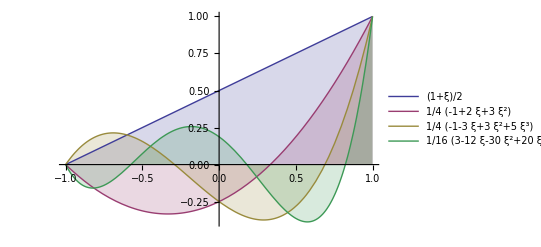

```mathematica
Plot[Evaluate[Subscript[Radau, left]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Subscript[Radau, right]= Table[(-1)^k/2(Subscript[p, k]-Subscript[p, k-1]),{k,1,4}]//Simplify;
```

```mathematica
Table[Subscript[R, L,i]= Subscript[Radau, left][[i]],{i,1,4}];
```

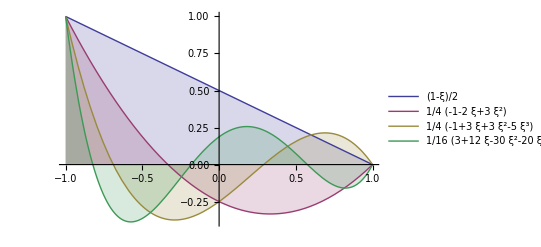

```mathematica
Plot[Evaluate[Subscript[Radau, right]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, R,i]= Subscript[Radau, right][[i]],{i,1,4}];
```

Observe that Radau Polynomials full fill the above requirements very easily:

```mathematica
Subscript[R, R,4]/.ξ->-1
Subscript[R, R,4]/.ξ->1
```

1

0

```mathematica
Subscript[R, L,4]/.ξ->-1
Subscript[R, L,4]/.ξ->1
```

0

1

Therefore the Radau_right is a great candidate for g_LB.
and Radau_left is a great candidate for g_RB.

Evaluating the derivative of g_LB and g_RB in every solution points, we observe:

```mathematica
Subscript[dg, LB] = D[Subscript[R, R,4],ξ]/.ξ->abscissas//N;
Subscript[dg, RB] = D[Subscript[R, L,4],ξ]/.ξ->abscissas//N;
Transpose[{Subscript[dg, LB]}]
Transpose[{Subscript[dg, RB]}]
```

{{-4.38915},{1.24762},{-0.614528},{0.327485}}

{{-0.327485},{0.614528},{-1.24762},{4.38915}}

```mathematica
Subscript[dg, RB] == -Reverse[Subscript[dg, LB]]
```

True

Because of symmetry, we only need to consider ℊ_LB(x), or simply ℊ(x). It is more convenient to consider the correction function in the standar element g(ξ) on [-1,1]. It is claimed that using special Polynomials such as Radau and Legendre polynomials, the DG, SD (or SD/SV) methods can be succesfully recovered.

## Putting everything to work toguether

Based on Shu’s paper, the Continuous Flux Polynomial, F_j(ξ), must satisfy the following conditions:

1. The continuous Flux function F_j(ξ) should use the information of the flux at both side of every element  I_j face, namely 	F_j[-1] = (f̂)_(j-1/2) and F_j[1] =(f̂)_(j+1/2)	(Perform upwind in the least case)
2. In each cell I_j, F_k(ξ) must be order K. i.e., one order higher than the solution polynomial u_j(ξ).
3. F_j(ξ) is required to approximate the discontinuous flux function f_j(ξ), i.e.,  F_j(ξ) - f_j(ξ) ≈ 0.

The continuous Flux function, F_j(ξ) is then proposed to be:

```mathematica
(* Subscript[F, j][ξ] = Subscript[f, j][ξ]+(Subscript[f̂, j-1/2]-Subscript[f, j][-1])Subscript[ℊ, LB][ξ]+(Subscript[f̂, j+1/2]-Subscript[f, j][1])Subscript[ℊ, RB][ξ] *)
```

However we are interested in the derivative of dF_j(ξ_k):

```mathematica
Subscript[dF, j] = Transpose[Subscript[df, j]] + Transpose[{Subscript[dg, LB]}].{SuperPlus[Subscript[f̂, j-1/2]]- SuperPlus[Subscript[f, j-1/2]]} + Transpose[{Subscript[dg, RB]}].{SuperMinus[Subscript[f̂, j+1/2]]- SuperMinus[Subscript[f, j+1/2]]} // TableForm
```

0.160282 | 0.161303 | 0.0624811 | -0.0804569 | -0.166919 | -0.153436 | -0.0846951 | -0.0218353 | 0.0291149 | 0.094688
0.169548 | 0.144361 | 0.0249548 | -0.112297 | -0.172727 | -0.137909 | -0.0662629 | -0.008384 | 0.0443831 | 0.114126
0.172671 | 0.112267 | -0.024948 | -0.14432 | -0.169488 | -0.11407 | -0.0443527 | 0.00837728 | 0.0662216 | 0.137849
0.167053 | 0.0805126 | -0.0625243 | -0.161429 | -0.160442 | -0.0948214 | -0.0291706 | 0.0218785 | 0.0848207 | 0.153596

Now we are ready to evolve the u_(j,k) by using the following ODE
					∂_t u = Δt/JdF_j(ξ_k)
End of Implementation in one dimension.

Manuel Diaz, KU, August 2013.